### Hexagonal Grid

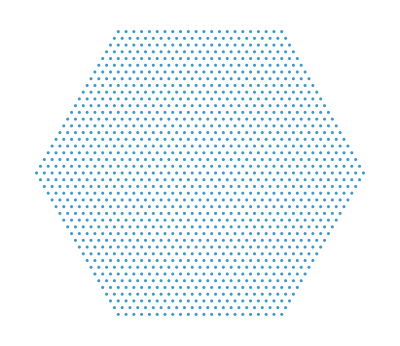

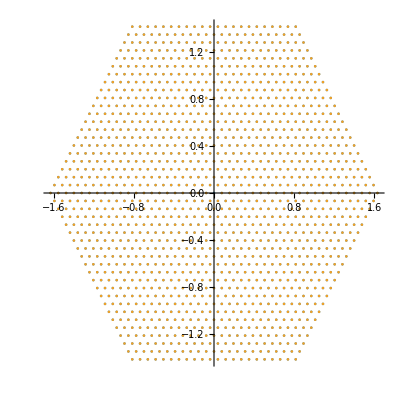

```mathematica
ℛUC=Polygon[1/(√3)Table[({Cos[2 Pi k/6+0π/2],Sin[2 Pi k/6+0π/2]}),{k,6}]];

h[x_,y_,0]:=Prepend[Table[{Cos[2 Pi k/6+0π/2]+x,Sin[2 Pi k/6+0π/2]+y},{k,6}],{0,0}]

h[x_,y_,n_]:=DeleteDuplicates[Flatten[Table[{Cos[2 Pi k/6+0π/2]+#1,Sin[2 Pi k/6+0π/2]+#2},{k,6}]&@@@h[x,y,n-1],1]]


ΛN=20;
(*ΛN=55; *)(* For the paper plots *)
UCmesh=2 √2 1/(√3)h[0,0,ΛN]/(ΛN+1);
kList=DeleteCases[UCmesh,{0,0}];
Show[Graphics[{EdgeForm[Thick],Transparent,ℛUC}],ListPlot[UCmesh,AspectRatio->1]]
ListPlot[{UCmesh,kList},AspectRatio->1]
```

### Parameters

```mathematica
w1=1;
w0=0.75w1;
μ=0.5;
mv=-0.5;
epsx=0.5;
epsy=-0.5;
a=1.42Sqrt[3];
thetaTwist=1.05Degree;
Ktheta=(4 Pi/(3 a)) 2 Sin[thetaTwist/2];
q0=Ktheta {0.3,0.4}√2;
qList=Table[RotationMatrix[2 Pi n/3].q0,{n,0,2}];

G[1]={0,0};

G[2]=(4 Pi/(3 a)) {-3/2,Sqrt[3]/2};

G[3]=(4 Pi/(3 a)) {-3/2,-Sqrt[3]/2};
```

#### Order parameter form

```mathematica
DeltaT[k_]:=1w1;
DeltaS[k_]:=1w1(0+1(k[[1]]+I k[[2]]));
```

### Functions

```mathematica
(*Things ending with T denote functions representing the tip, functions ending with s denote functions representing the sample*)
ξT[k_,τ_]:=-μ+Norm[k];
ξS[k_,τ_]:=-μ+Norm[k];

DispersionS[k_,Δ_,τ_]:=Sqrt[ξS[k,τ]^2+Abs[Δ]^2];
DispersionT[k_,Δ_,τ_]:=Sqrt[ξT[k,τ]^2+Abs[Δ]^2];

uT[k_, Δ_, τ_]:=Sqrt[1/2(1+ξT[k,τ]/DispersionT[k,Δ,τ])];
uS[k_,Δ_,τ_]:=Sqrt[1/2(1+ξS[k,τ]/DispersionS[k,Δ,τ])];
vT[k_,Δ_,τ_]:=If[Δ==0,0,Conjugate[Δ]/Abs[Δ]*Sqrt[1/2 (1-ξT[k,τ]/DispersionT[k,Δ,τ])]];

vS[k_,Δ_,τ_]:=If[Δ==0,0,Conjugate[Δ]/Abs[Δ]*Sqrt[1/2 (1-ξS[k,τ]/DispersionS[k,Δ,τ])]];
th[k_]:=ArcTan[k[[1]],k[[2]]];

phi[j_]:=2Pi(j-1)/3;
(*Simplified form of M derived from analytically simplifying <Psi^BdG_T(k+q)|T|Psi^BdG_S(k)>*)
M[k_,q_,r_,τ_]:=Module[{kp,thetaK,thetaKp,thetaDelta,thetaSigma},
kp=k+q;
thetaK=th[k];
thetaKp=th[kp];
thetaDelta=(thetaK-thetaKp)/2;
thetaSigma=(thetaK+thetaKp)/2;
Sum[uT[kp,DeltaT[kp],τ]*uS[k,DeltaS[k],τ]*(w0*Cos[thetaDelta]+w1*τ*Cos[τ*phi[j]+thetaSigma])*Exp[I*τ*G[j].r]-Conjugate[vT[kp,DeltaT[kp],τ]]*vS[k,DeltaS[k],τ]*(w0*Cos[thetaDelta]+w1*τ*Cos[τ*phi[j]+thetaSigma])*Exp[I*τ*G[j].r],{j,1,3}]]
M[k_,{},r_,τ_,lambda_]:=0;

IntegrandPLUS[k_,q_,r_]:=(Abs[M[k,q,r,1]]^2)
IntegrandMINUS[k_,q_,r_]:=Abs[M[k,-q,r,-1]]^2
dk=0.001;

(*Calculates \int_k,q |M(k,q,tau=1,r)|^2+|M(k,q,tau=-1,r)|^2*)
Signal[r_]:=Sum[IntegrandPLUS[k,q,r]+IntegrandMINUS[k,q,r],{k,kList},{q,qList}]
```

### PLotting

```mathematica
data=Table[{rx,ry,Signal[{rx,ry}]},{rx,-Pi,Pi,2 Pi/24},{ry,-Pi,Pi,2 Pi/24}];
```

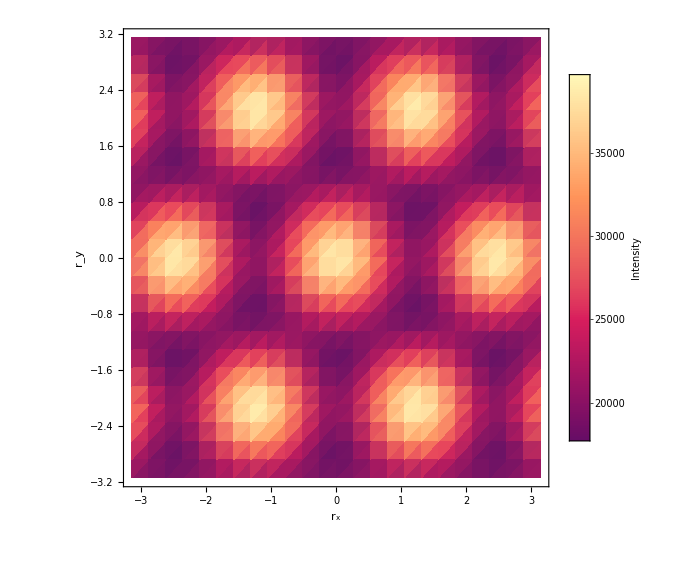

```mathematica
values=data[[All,All,3]];

ListDensityPlot[Transpose[values],DataRange->{{-Pi,Pi},{-Pi,Pi}},PlotRange->All,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{Style[TraditionalForm[Subscript[r,x]],24,FontFamily->"Times New Roman",Black],Style[TraditionalForm[Subscript[r,y]],24,FontFamily->"Times New Roman",Black]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Intensity",18,FontFamily->"Times New Roman",Black],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],Right],ImageSize->Large]
```